### γ_1=γ_2

```mathematica
f1[p_]:=γ(1+ⅇ^α)/(1+Exp[-(β (1+p(n-1))/n-α)])-κ;
f2[p_]:=γ(1+ⅇ^α)/(1+Exp[-(β (p(n-1))/n-α)]);
```

```mathematica
Series[f1[0]-f2[0],{γ,0,1}]//FullSimplify//Normal

Series[f1[1]-f2[1],{γ,0,1}]//FullSimplify//Normal
```

(-1+(1+ⅇ^α)/(1+ⅇ^(α-β/n))) γ-κ

(1+ⅇ^α) (1/(1+ⅇ^(α-β))-1/(1+ⅇ^(α+(-1+1/n) β))) γ-κ

```mathematica
FP[n_,α_,β_]:=Module[
{
Δ0,Δ1,,f1,f2,γ,κ
,root,AllRoots,case
},
γ=1.0;
κ=0.1;
Δ0=(-1+(1+ⅇ^α)/(1+ⅇ^(α-β/n))) γ-κ;
Δ1=(1+ⅇ^α) (1/(1+ⅇ^(α-β))-1/(1+ⅇ^(α+(-1+1/n) β))) γ-κ;
f1[p_]:=γ(1+ⅇ^α)/(1+Exp[-(β (1+p(n-1))/n-α)])-κ;
f2[p_]:=γ(1+ⅇ^α)/(1+Exp[-(β (p(n-1))/n-α)]);

(*root[x0_]:=Module[{r},
r=FindRoot[
p(1-p)(f1[p]-f2[p])==0,{p,0.5}
];
If[r⟦1,2⟧<0,0,If[r⟦1,2⟧>1.0,1.0,r⟦1,2⟧]]
];
AllRoots=Round[root[#],0.0001]&/@Range[0.05,0.95,0.05];
DeleteDuplicates[AllRoots]*)
Which[
(Δ0>0&&Δ1>0),outcome={"Dominance of P",1},
(Δ0>0&&Δ1<0),outcome={"Coexistence",2},
(Δ0<0&&Δ1<0),outcome={"Dominance of N",3},
(Δ0<0&&Δ1>0),outcome={"Bi-Stabillity",4}
];
{Δ0,Δ1,outcome}

](*END of MODULE*)

FP[#,1.0,10.0]&/@{5.,155.}
```

{{1.61828,-0.0970713,{Coexistence,2}},{-0.0521381,-0.0999694,{Dominance of N,3}}}

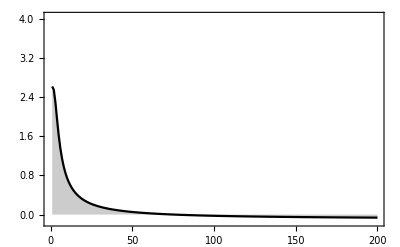

```mathematica
ListPlot[
{#,FP[#,1.0,10.0]⟦1⟧}&/@Range[1,200,1]
,PlotRange->{All,{-0.15,4.05}}
,Filling->Axis
,Frame->True
,PlotStyle->{Black}
,Joined->True
]
```

#### n=5

```mathematica
t=Table[
FP[5,α,β]⟦3,2⟧
,{β,0,5,0.01}
,{α,0,5,0.01}
];

colors="CherryTones";

Lt=t//Length;
tPlot=Table[t⟦Lt-i+1,j⟧,{i,1,Lt},{j,1,Lt}];
ArrayPlot[
tPlot
,ColorFunction->(Opacity[0.8,ColorData[colors][1-#1]]&)
,ColorFunctionScaling->True
,Background->White
,Frame->True
,AspectRatio->0.95
,ImageSize->400
,FrameStyle->Directive[Thickness[0.0035],Black]
,LabelStyle->{FontSize->24,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
, FrameLabel -> {{"α","n=5"},{"β",None}}
,FrameTicks->{
{{1,"5"},{101,"4"},{201,"3"},{301,"2"},{401,"1"},{501,"0"}},{{1,"0"},{101,"1"},{201,"2"},{301,"3"},{401,"4"},{501,"5"}}
}
]

(*ListDensityPlot[t,Mesh->None,InterpolationOrder->0]*)
```

-Graphics-

#### n=10

```mathematica
t=Table[
FP[10,α,β]⟦3,2⟧
,{β,0,5,0.01}
,{α,0,5,0.01}
];

colors="CherryTones";

Lt=t//Length;
tPlot=Table[t⟦Lt-i+1,j⟧,{i,1,Lt},{j,1,Lt}];
ArrayPlot[
tPlot
,ColorFunction->(Opacity[0.8,ColorData[colors][1-#1]]&)
,ColorFunctionScaling->True
,Background->White
,Frame->True
,AspectRatio->0.95
,ImageSize->400
,FrameStyle->Directive[Thickness[0.0035],Black]
,LabelStyle->{FontSize->24,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
, FrameLabel -> {{"α","n=10"},{"β",None}}
,FrameTicks->{
{{1,"5"},{101,"4"},{201,"3"},{301,"2"},{401,"1"},{501,"0"}},{{1,"0"},{101,"1"},{201,"2"},{301,"3"},{401,"4"},{501,"5"}}
}
]

(*ListDensityPlot[t,Mesh->None,InterpolationOrder->0]*)
```

-Graphics-

#### n=25

```mathematica
t=Table[
FP[25,α,β]⟦3,2⟧
,{β,0,5,0.01}
,{α,0,5,0.01}
];
colors="CherryTones";

Lt=t//Length;
tPlot=Table[t⟦Lt-i+1,j⟧,{i,1,Lt},{j,1,Lt}];
ArrayPlot[
tPlot
,ColorFunction->(Opacity[0.8,ColorData[colors][1-#1]]&)
,ColorFunctionScaling->True
,Background->White
,Frame->True
,AspectRatio->0.95
,ImageSize->400
,FrameStyle->Directive[Thickness[0.0035],Black]
,LabelStyle->{FontSize->24,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
, FrameLabel -> {{"α","n=25"},{"β",None}}
,FrameTicks->{
{{1,"5"},{101,"4"},{201,"3"},{301,"2"},{401,"1"},{501,"0"}},{{1,"0"},{101,"1"},{201,"2"},{301,"3"},{401,"4"},{501,"5"}}
}
]
(*ListDensityPlot[t,Mesh->None,InterpolationOrder->0]*)
```

-Graphics-

#### n=50

```mathematica
t=Table[
FP[50,α,β]⟦3,2⟧
,{β,0,5,0.01}
,{α,0,5,0.01}
];

colors="CherryTones";

Lt=t//Length;
tPlot=Table[t⟦Lt-i+1,j⟧,{i,1,Lt},{j,1,Lt}];
ArrayPlot[
tPlot
,ColorFunction->(Opacity[0.8,ColorData[colors][1-#1]]&)
,ColorFunctionScaling->True
,Background->White
,Frame->True
,AspectRatio->0.95
,ImageSize->400
,FrameStyle->Directive[Thickness[0.0035],Black]
,LabelStyle->{FontSize->24,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
, FrameLabel -> {{"α","n=50"},{"β",None}}
,FrameTicks->{
{{1,"5"},{101,"4"},{201,"3"},{301,"2"},{401,"1"},{501,"0"}},{{1,"0"},{101,"1"},{201,"2"},{301,"3"},{401,"4"},{501,"5"}}
}
]

(*ListDensityPlot[t,Mesh->None,InterpolationOrder->0]*)
```

-Graphics-

### Graph Legends

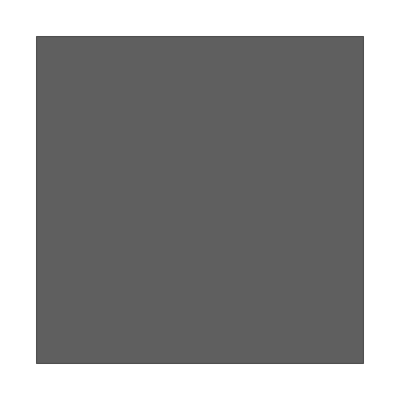

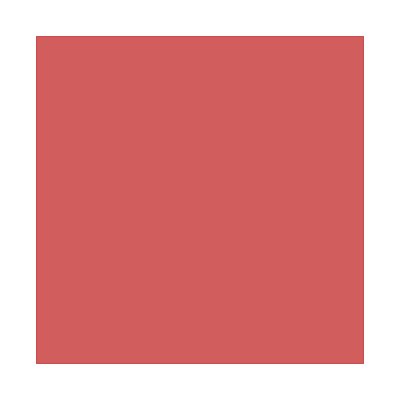

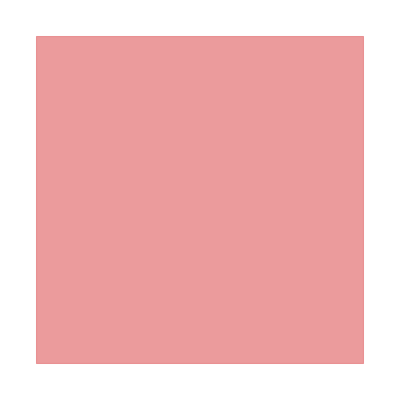

-Graphics-

```mathematica
Graphics[{EdgeForm[Thick],Opacity[0.8,ColorData["CherryTones"][0]],Rectangle[]}]
Graphics[{EdgeForm[Thick],Opacity[0.8,ColorData["CherryTones"][1/3]],Rectangle[]}]
Graphics[{EdgeForm[Thick],Opacity[0.8,ColorData["CherryTones"][2/3]],Rectangle[]}]
Graphics[{EdgeForm[Thick],Opacity[0.8,ColorData["CherryTones"][1]],Rectangle[]}]
```